```mathematica
n=10;
α=.01;
β=0;
```

```mathematica
Q[0]=Table[RandomInteger[{1,1000}],{i,1,n}]
```

{582,849,77,528,118,785,819,901,773,742}

```mathematica
x=Table[{RandomReal[{0,100}],RandomReal[{0,100}]},{i,1,n}];
d=Table[EuclideanDistance[x[[i]],x[[j]]],{i,1,n},{j,1,n}];
```

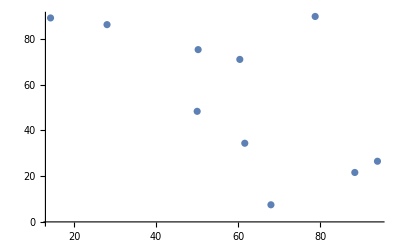

```mathematica
ListPlot[x,PlotRange->All]
```

```mathematica
M1[Q_]:=α*Table[If[j≠i,Boole[Q[[j]]<Q[[i]]]/d[[i,j]],0],{i,1,n},{j,1,n}]
M2[Q_]:=-α*Table[If[j==i,Sum[If[k≠i,Boole[Q[[k]]>Q[[i]]]/d[[i,k]],0],{k,1,n}],0],{i,1,n},{j,1,n}]
M3[Q_]:=β*IdentityMatrix[n]
```

```mathematica
M[Q_]:=M1[Q]+M2[Q]+M3[Q]
```

```mathematica
TraditionalForm[M[Q[0]]]
```

(-0.00200952 | 0. | 0.000403883 | 0.000370989 | 0.000151798 | 0. | 0. | 0. | 0. | 0.
0.000906784 | -0.000156387 | 0.000279525 | 0.00040091 | 0.000176084 | 0.000179451 | 0.000380713 | 0. | 0.000201651 | 0.000273025
0. | 0. | -0.00231914 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.000228374 | -0.00213373 | 0.000213614 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.000113065 | 0. | -0.00287862 | 0. | 0. | 0. | 0. | 0.
0.000152672 | 0. | 0.000112427 | 0.000203743 | 0.00135328 | -0.000643789 | 0. | 0. | 0.00009865 | 0.000300252
0.000312421 | 0. | 0.000196479 | 0.000198218 | 0.000145295 | 0.000153758 | -0.000501255 | 0. | 0.000154918 | 0.000172503
0.000142734 | 0.000156387 | 0.000113302 | 0.000224175 | 0.0004024 | 0.000310579 | 0.000120542 | 0. | 0.000102334 | 0.000361901
0.000259289 | 0. | 0.00071012 | 0.000184346 | 0.0000996868 | 0. | 0. | 0. | -0.000557553 | 0.000138162
0.000235622 | 0. | 0.000161962 | 0.00055135 | 0.000336456 | 0. | 0. | 0. | 0. | -0.00124584)

```mathematica
Eigenvalues[M[Q[0]]]
```

{-0.00287862,-0.00231914,-0.00213373,-0.00200952,-0.00124584,-0.000643789,-0.000557553,-0.000501255,-0.000156387,0.}

```mathematica
Q[t_]=FullSimplify[MatrixExp[t*M[Q[0]]].Q[0]];
```

```mathematica
Limit[Q[t],t->Infinity]
```

{2.56082×10^-14,1.50595×10^-12,2.96843×10^-14,5.02766×10^-15,-6.89419×10^-14,-7.78294×10^-13,7.85677×10^-13,6174.,3.79515×10^-13,-3.6363×10^-14}

```mathematica
Manipulate[ListPlot[Reverse[Sort[N[Q[t]]]],PlotRange->All],{t,0,10000,.1}]
```

```mathematica
findRankSwitch[max_]:=Module[{T={0},t0=0,delT=.1},

While[t0≤max,
If[!DuplicateFreeQ[Round[Q[t0],.01]]&&DuplicateFreeQ[Round[Q[t0+delT],.01]],
AppendTo[T,Last[T]+t0];
Q[t_]=FullSimplify[MatrixExp[t*M[Q[t0]]].Q[t0]];
t0=0;
];
t0+=delT;
];
Return[T];
]
```

```mathematica
findRankSwitch[1000]
```

{0,310.1,320.2,330.5,340.9,351.6,362.,370.4,379.,1163.2,1167.1,1171.1,1175.1,1179.1,1183.2,1187.,1189.6,1376.7,1464.3,1572.1,1714.2,1924.2,2437.7,2437.9}

```mathematica
Q[t_]=FullSimplify[MatrixExp[t*M[Q[10.1]]].Q[10.1]];
```

```mathematica
Sort[Q[330.5-320.2]]
```

{-2.09194,0.44501,0.450473,0.89929,1.7499,5.67328,7.02586,15.1776,20.6864,28.6044}

```mathematica
Sort[Q[310.1]]
```

{-2.14646,0.465086,0.47452,0.946153,1.78456,5.82534,7.25429,15.2095,20.4621,28.3452}